```mathematica
means={2694.77,1974.84,2627.28,2869.01,3133.86,3424.65,3039.35,3005.26,3358.64};
stds={235.8525,234.358,201.0125,239.6005,255.4105,279.421,218.042,267.2015,237.6005};
meansnorm=means/Mean[means]
stdsnorm=stds/Mean[means]
data=MapThread[Around,{meansnorm,stdsnorm}];
comparisons=Table[{1,i},{i,2,9}];
verticalOffset=500/Mean[means];
```

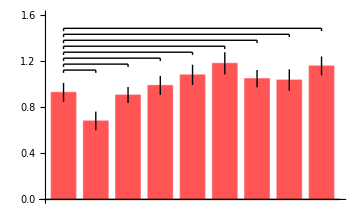

```mathematica
topY=Max[MapThread[Plus,{meansnorm,stdsnorm}]];
startY=topY-450/Mean[means];
lineSpacing=150/Mean[means];
comparisonLines=Table[Module[{x1=comp[[1]],x2=comp[[2]],y=startY+lineSpacing*(i-1)},{Line[{{x1,y},{x2,y}}],Line[{{x1,y},{x1,y-70/Mean[means]}}],Line[{{x2,y},{x2,y-70/Mean[means]}}]}],{i,Length[comparisons]},{comp,{comparisons[[i]]}}]//Flatten;
BarChart[data,ChartStyle->Lighter[Red],BarSpacing->0.3,Epilog->comparisonLines,LabelStyle->{Black,14},ImageSize->Medium, PlotRange->{Automatic,{0,1.6}}]
```

```mathematica
YFPmeans={223.1466667,234.358,201.0125,239.6005,255.4105,279.421,218.042,267.2015,237.6005};
YFPstds={56.05280144,58.99733397,47.36827186,56.19591947,61.10223535,52.95253808,54.18583021,58.13628224,56.14572909};
YFPmeansnorm=YFPmeans/Mean[YFPmeans]
YFPstdsnorm=YFPstds/Mean[YFPmeans]
YFPdata=MapThread[Around,{YFPmeansnorm,YFPstdsnorm}];
YFPcomparisons=Table[{1,i},{i,2,9}];
```

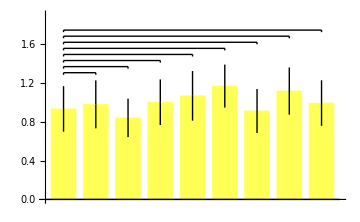

```mathematica
YFPtopY=Max[MapThread[Plus,{YFPmeansnorm,YFPstdsnorm}]];
YFPstartY=YFPtopY-20/Mean[YFPmeans];
YFPlineSpacing=15/Mean[YFPmeans];
YFPcomparisonLines=Table[Module[{x1=comp[[1]],x2=comp[[2]],y=YFPstartY+YFPlineSpacing*(i-1)},{Line[{{x1,y},{x2,y}}],Line[{{x1,y},{x1,y-5/Mean[YFPmeans]}}],Line[{{x2,y},{x2,y-5/Mean[YFPmeans]}}]}],{i,Length[YFPcomparisons]},{comp,{YFPcomparisons[[i]]}}]//Flatten;
BarChart[YFPdata,ChartStyle->Lighter[Yellow],BarSpacing->0.3,Epilog->YFPcomparisonLines,LabelStyle->{Black,14},ImageSize->Medium, PlotRange->{Automatic,{0,1.9}}]
```

```mathematica
means630={909.88325,861.975,891.1960294,986.3016667,871.7750769,1006.758621,832.3205,809.10725,749.427};
stds630={176.883875,160.4766667,213.1054412,201.374,140.958,238.3872414,159.01,190.3675,135.531};
means630norm=means630/Mean[means630]
stds630norm=stds630/Mean[means630]
data630=MapThread[Around,{means630norm,stds630norm}];
comparisons630=Table[{1,i},{i,2,9}];
verticalOffset630=500/Mean[means630];
```

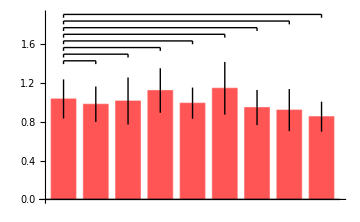

```mathematica
topY630=Max[MapThread[Plus,{means630norm,stds630norm}]];
startY630=topY630+10/Mean[means630];
lineSpacing630=60/Mean[means630];
comparisonLines630=Table[Module[{x1=comp[[1]],x2=comp[[2]],y=startY630+lineSpacing630*(i-1)},{Line[{{x1,y},{x2,y}}],Line[{{x1,y},{x1,y-30/Mean[means630]}}],Line[{{x2,y},{x2,y-30/Mean[means630]}}]}],{i,Length[comparisons630]},{comp,{comparisons630[[i]]}}]//Flatten;
BarChart[data630,ChartStyle->Lighter[Red],BarSpacing->0.3,Epilog->comparisonLines630,LabelStyle->{Black,14},ImageSize->Medium, PlotRange->{Automatic,{0,1.9}}]
```

```mathematica
YFPmeans630={201.3436282,235.9506596,208.1467935,247.9091156,243.766818,253.2522524,195.6391134,269.180659,192.2611874};
YFPstds630={32.18111448,38.82297108,30.85370249,44.25991432,38.94367678,108.0054931,24.19292789,43.01488613,29.07369209};
YFPmeans630norm=YFPmeans630/Mean[YFPmeans630]
YFPstds630norm=YFPstds630/Mean[YFPmeans630]
YFPdata630=MapThread[Around,{YFPmeans630norm,YFPstds630norm}];
YFPcomparisons630=Table[{1,i},{i,2,9}];
```

{0.885048,1.03717,0.914953,1.08974,1.07153,1.11322,0.859973,1.18324,0.845125}

{0.141459,0.170655,0.135624,0.194554,0.171185,0.474761,0.106345,0.189081,0.1278}

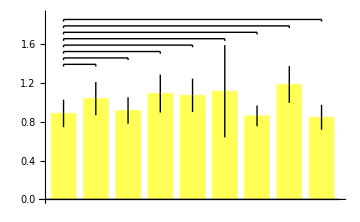

```mathematica
YFPtopY630=Max[MapThread[Plus,{YFPmeans630norm,YFPstds630norm}]];
YFPstartY630=YFPtopY630-45/Mean[YFPmeans630];
YFPlineSpacing630=15/Mean[YFPmeans630];

YFPcomparisonLines630=Table[Module[{x1=comp[[1]],x2=comp[[2]],y=YFPstartY630+YFPlineSpacing630*(i-1)},{Line[{{x1,y},{x2,y}}],Line[{{x1,y},{x1,y-5/Mean[YFPmeans630]}}],Line[{{x2,y},{x2,y-5/Mean[YFPmeans630]}}]}],{i,Length[YFPcomparisons630]},{comp,{YFPcomparisons630[[i]]}}]//Flatten;
BarChart[YFPdata630,ChartStyle->Lighter[Yellow],BarSpacing->0.3,Epilog->YFPcomparisonLines630,LabelStyle->{Black,14},ImageSize->Medium, PlotRange->{Automatic,{0,1.9}}]
```